========================================

SIMULATION 1: MASS 1

========================================

Target: (-0.1, 4.1)

Pickup angles: {-26.7,-9.,11.3,30.}°

Simulating...

✓ SIMULATION 1 SUCCESS!

========================================

SIMULATION 2: MASS 2

========================================

Target: (-0.1, 4.255)

Pickup angles: {-15.4,-6.4,3.4,24.2}°

Simulating...

✓ SIMULATION 2 SUCCESS!

========================================

SIMULATION 3: MASS 3

========================================

Target: (-0.12, 4.222)

Pickup angles: {-20.,-6.1,9.2,23.5}°

Simulating...

✓ SIMULATION 3 SUCCESS!

========================================

SIMULATION 4: MASS 4

========================================

Target: (0.025, 4)

Pickup angles: {-32.2,-12.7,10.,33.9}°

Simulating 4...

✓ SIMULATION 4 SUCCESS!

========================================

ALL 4 SIMULATIONS COMPLETE!

========================================

Target locations:

Mass 1: (-0.1, 4.1)

Mass 2: (-0.1, 4.255)

Mass 3: (-0.12, 4.222)

Mass 4: (0.025, 4)

Legend:

- animation1: Mass 1 (Red)

- animation2: Mass 2 (Green)

- animation3: Mass 3 (Blue)

- animation4: Mass 4 (Purple)

========================================

MASTER SEQUENTIAL ANIMATION

========================================

tCycle = 11. seconds

tTotal = 44. seconds

========================================

ANALYSIS PLOTS SUMMERY

========================================

1. torquePlot1 - Control torques for Mass 1

2. errorPlot1 - Tracking error for Mass 1

3. paramErrorPlot - Parameter estimation error

4. jointAnglesPlot - Joint angles for all 4 masses

5. torqueComparisonPlot - Joint 1 torque across all masses

Key observations:

- Torque jumps at t=5.s show controller responding to mass pickup

- Parameter error = 0.6 kg (controller underestimates)

- Tracking error spikes briefly then converges (adaptive behavior)

- All 4 simulations show similar adaptive behavior

========================================

Plot 1: Control Torques - Mass 1

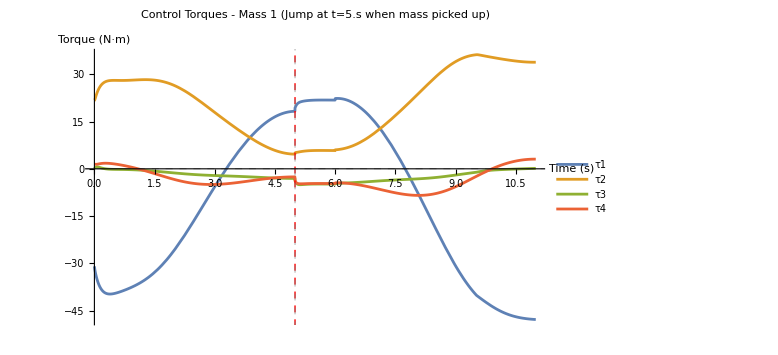

Plot 2: Tracking Error - Mass 1

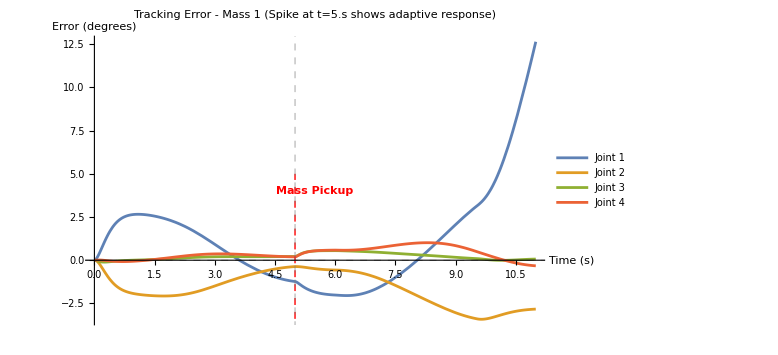

Plot 3: Parameter Estimation Error

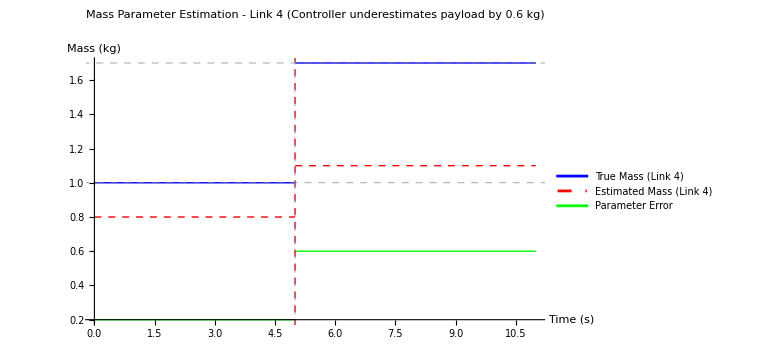

Plot 4: Joint Angles - All 4 Masses

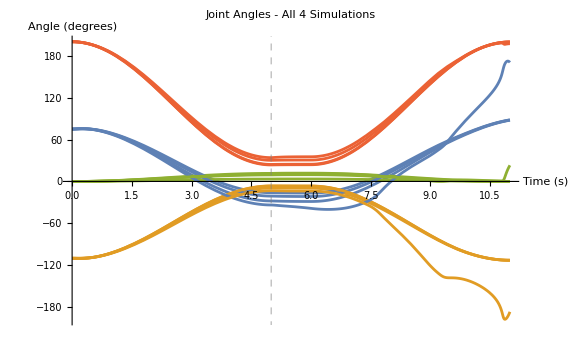

Plot 5: Torque Comparison - Joint 1 Across All Masses

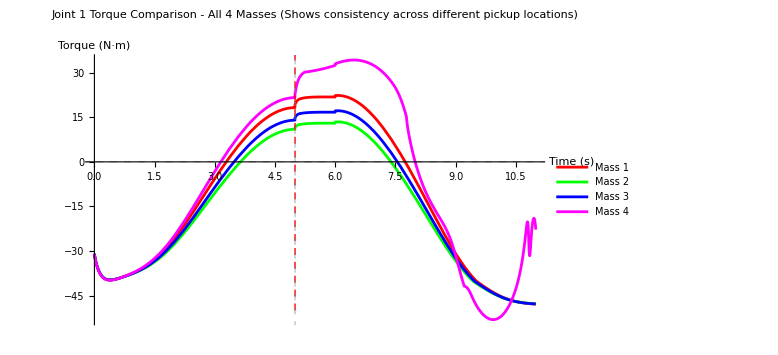

```mathematica
ClearAll["Global`*"];

(* ========================================SHARED CONSTANTS========================================*)
limm=0.25;
Sat[x_]:=Piecewise[{{x/limm,Abs[x]<limm},{-1,x<=-limm},{1,x>=limm}}];
SmoothStep[t_,t0_,t1_]:=Piecewise[{{0,t<t0},{1,t>t1},{(1-Cos[Pi*(t-t0)/(t1-t0)])/2,t0<=t<=t1}}];

n=4;
linkLength=1.10;
diamondWidth=2.5;
diamondHeight=5.0;
diamondYOffset=1.25;
diamondCenterY=diamondHeight/2;
entryGap=1.5; (*Width of the opening at the bottom*)

(*Define vertices as an OPEN chain:Start Left of gap->Top->End Right of gap*)
diamondVertices={{-entryGap/2,diamondYOffset},(*Left Gate Post*){-diamondWidth,diamondCenterY+diamondYOffset},(*Left Tip*){0,diamondHeight+diamondYOffset},(*Top Tip*){diamondWidth,diamondCenterY+diamondYOffset},(*Right Tip*){entryGap/2,diamondYOffset}                            (*Right Gate Post*)};

baseX=0;
baseY=0;
massPerLink=1.0;
linkLengthNum=1.0;
gNum=9.81;
payloadMass=.7;
massEstimates=Table[0.8,{i,n}];
payloadEstimate=0.3;

tIngress=5.0;
tHold=1.0;
tEgress=5.0;
tCycle=tIngress+tHold+tEgress;

homeAngles={75,-110,0,200}*Degree;

(* ================================================================*)
(*SIMULATION 1-MASS 1 AT (-0.10,4.0)-THE WORKING TARGET*)
(* ================================================================*)
Print["========================================"];
Print["SIMULATION 1: MASS 1"];
Print["========================================\n"];

targetX1=-0.10;
targetY1=4.1;

Print["Target: (",targetX1,", ",targetY1,")"];

xTip1[th1_,th2_,th3_,th4_]:=baseX-linkLength*(Sin[th1]+Sin[th2]+Sin[th3]+Sin[th4]);
yTip1[th1_,th2_,th3_,th4_]:=baseY+linkLength*(Cos[th1]+Cos[th2]+Cos[th3]+Cos[th4]);

solution1=NMinimize[{(xTip1[t1,t2,t3,t4]-targetX1)^2+(yTip1[t1,t2,t3,t4]-targetY1)^2,-Pi/2<t1<Pi/2,-Pi/2<t2<Pi/2,-Pi/2<t3<Pi/2,-Pi/2<t4<Pi/2},{t1,t2,t3,t4}];

pickupAngles1={t1,t2,t3,t4}/. solution1[[2]];
Print["Pickup angles: ",Round[pickupAngles1*180/Pi,0.1],"°\n"];

qdes1=Table[Piecewise[{{homeAngles[[i]]+(pickupAngles1[[i]]-homeAngles[[i]])*SmoothStep[t,0,tIngress],t<=tIngress},{pickupAngles1[[i]],tIngress<t<=tIngress+tHold},{pickupAngles1[[i]]+(homeAngles[[i]]-pickupAngles1[[i]])*SmoothStep[t,tIngress+tHold,tIngress+tHold+tEgress],t>tIngress+tHold}}],{i,n}];

xj1[0]=baseX;
yj1[0]=baseY;
Do[xj1[i]=baseX+Sum[-linkLength*Sin[θ1[j][t]],{j,1,i}],{i,1,n}];
Do[yj1[i]=baseY+Sum[linkLength*Cos[θ1[j][t]],{j,1,i}],{i,1,n}];
Do[xb1[i]=baseX+xj1[i-1]-baseX-linkLength/2*Sin[θ1[i][t]],{i,1,n}];
Do[yb1[i]=baseY+yj1[i-1]-baseY+linkLength/2*Cos[θ1[i][t]],{i,1,n}];

Do[Mj1[i]=1/12*m1[i]*l1[i]^2,{i,n}];

T1=Sum[1/2*m1[i]*(D[xb1[i],t]^2+D[yb1[i],t]^2)+1/2*Mj1[i]*(D[θ1[i][t],t])^2,{i,n}];
V1=Sum[m1[i]*g1*yb1[i],{i,n}];
Lag1=T1-V1;
Eqs1=Table[D[D[Lag1,D[θ1[i][t],t]],t]-D[Lag1,θ1[i][t]],{i,n}];

MassM1=Table[Coefficient[Eqs1[[i]],D[θ1[j][t],{t,2}]],{i,n},{j,n}];
Cc1=Table[Sum[0.5*(D[MassM1[[i,j]],θ1[k][t]]+D[MassM1[[i,k]],θ1[j][t]]-D[MassM1[[j,k]],θ1[i][t]])*D[θ1[k][t],t],{k,n}],{i,n},{j,n}];
Gg1=Table[D[Eqs1[[i]],g1],{i,n}]*g1;

q1=Table[θ1[i][t],{i,n}];
qtilde1=q1-qdes1;
Lambda1=DiagonalMatrix[Table[4,{i,n}]];
dqr1=D[qdes1,t]-Lambda1.qtilde1;
s1=D[qtilde1,t]+Lambda1.qtilde1;

DynamicsLHS1=MassM1.D[dqr1,t]+Cc1.dqr1+Gg1;
Yy1=Table[D[DynamicsLHS1[[i]],m1[j]],{i,n},{j,n}];

hataa1=massEstimates;
kGain1=10.0;
controlGains1=DiagonalMatrix[Table[kGain1,{i,n}]];
SatVec1=Table[Sat[s1[[i]]],{i,n}];
ControlInput1=Yy1.hataa1-controlGains1.SatVec1;

numRules1[time_]:=Join[Table[m1[i]->massPerLink,{i,n-1}],{m1[n]->If[time>tIngress&&time<=(tIngress+tHold+tEgress),massPerLink+payloadMass,massPerLink]},Table[l1[i]->linkLengthNum,{i,n}],{g1->gNum}];

hataaDynamic1[time_]:=Join[Table[massEstimates[[i]],{i,n-1}],{If[time>tIngress&&time<=(tIngress+tHold+tEgress),massEstimates[[n]]+payloadEstimate,massEstimates[[n]]]}];

ics1=Join[Table[θ1[i][0]==homeAngles[[i]],{i,n}],Table[Derivative[1][θ1[i]][0]==0,{i,n}]];

ControlInputDynamic1=Yy1.hataaDynamic1[t]-controlGains1.SatVec1;
EqsN1=Thread[Eqs1==ControlInputDynamic1]/. numRules1[t];

Print["Simulating..."];
solDE1=NDSolve[Join[EqsN1,ics1],Table[θ1[i][t],{i,n}],{t,0,tCycle},Method->{"EquationSimplification"->"Residual"},MaxSteps->10000];

If[Length[solDE1]>0,Print["✓ SIMULATION 1 SUCCESS!\n"],Print["✗ SIMULATION 1 FAILED!\n"];Abort[]];


diamondBoundary1=Graphics[{Thickness[0.005],Red,Dashed,Line[diamondVertices]}];

robotGraphics1[time_]:=Module[{links,joints,endPoint,massPosition,massPoint},links=Table[{Thickness[0.01],Black,Line[{{xj1[k-1],yj1[k-1]},{xj1[k],yj1[k]}}/. solDE1/. t->time]},{k,1,n}];
joints=Table[{Blue,Disk[{xj1[k],yj1[k]}/. solDE1/. t->time,0.08]},{k,0,n}];
endPoint={Orange,PointSize[0.025],Point[{xj1[n],yj1[n]}/. solDE1/. t->time]};
massPosition=If[time>(tIngress+tHold),{xj1[n],yj1[n]}/. solDE1/. t->time,{targetX1,targetY1}];
massPoint={Red,PointSize[0.03],Point[massPosition]};
Graphics[{links,joints,endPoint,massPoint}]];

baseMarker1=Graphics[{Gray,EdgeForm[Black],Thickness[0.015],Rectangle[{baseX-0.2,baseY-0.15},{baseX+0.2,baseY}],Black,Text["BASE",{baseX,baseY-0.25},BaseStyle->{FontSize->12,Bold}]}];

animation1=Animate[Show[diamondBoundary1,baseMarker1,robotGraphics1[time],PlotRange->{{-diamondWidth-0.5,diamondWidth+0.5},{-0.5,diamondHeight+diamondYOffset+0.5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Mass 1 at ("<>ToString[targetX1]<>", "<>ToString[targetY1]<>")\nt="<>ToString[NumberForm[time,{3,1}]]<>"s",ImageSize->Large],{time,0,tCycle,0.05},AnimationRate->1];


(* ================================================================*)
(*SIMULATION 2-MASS 2 AT (-0.12,3.95)-VERY CLOSE TO WORKING*)
(* ================================================================*)
Print["========================================"];
Print["SIMULATION 2: MASS 2"];
Print["========================================\n"];

targetX2=-0.1;
targetY2=4.255;

Print["Target: (",targetX2,", ",targetY2,")"];

xTip2[th1_,th2_,th3_,th4_]:=baseX-linkLength*(Sin[th1]+Sin[th2]+Sin[th3]+Sin[th4]);
yTip2[th1_,th2_,th3_,th4_]:=baseY+linkLength*(Cos[th1]+Cos[th2]+Cos[th3]+Cos[th4]);

solution2=NMinimize[{(xTip2[t1,t2,t3,t4]-targetX2)^2+(yTip2[t1,t2,t3,t4]-targetY2)^2,-Pi/2<t1<Pi/2,-Pi/2<t2<Pi/2,-Pi/2<t3<Pi/2,-Pi/2<t4<Pi/3},{t1,t2,t3,t4}];

pickupAngles2={t1,t2,t3,t4}/. solution2[[2]];
Print["Pickup angles: ",Round[pickupAngles2*180/Pi,0.1],"°\n"];

qdes2=Table[Piecewise[{{homeAngles[[i]]+(pickupAngles2[[i]]-homeAngles[[i]])*SmoothStep[t,0,tIngress],t<=tIngress},{pickupAngles2[[i]],tIngress<t<=tIngress+tHold},{pickupAngles2[[i]]+(homeAngles[[i]]-pickupAngles2[[i]])*SmoothStep[t,tIngress+tHold,tIngress+tHold+tEgress],t>tIngress+tHold}}],{i,n}];

xj2[0]=baseX;
yj2[0]=baseY;
Do[xj2[i]=baseX+Sum[-linkLength*Sin[θ2[j][t]],{j,1,i}],{i,1,n}];
Do[yj2[i]=baseY+Sum[linkLength*Cos[θ2[j][t]],{j,1,i}],{i,1,n}];
Do[xb2[i]=baseX+xj2[i-1]-baseX-linkLength/2*Sin[θ2[i][t]],{i,1,n}];
Do[yb2[i]=baseY+yj2[i-1]-baseY+linkLength/2*Cos[θ2[i][t]],{i,1,n}];

Do[Mj2[i]=1/12*m2[i]*l2[i]^2,{i,n}];

T2=Sum[1/2*m2[i]*(D[xb2[i],t]^2+D[yb2[i],t]^2)+1/2*Mj2[i]*(D[θ2[i][t],t])^2,{i,n}];
V2=Sum[m2[i]*g2*yb2[i],{i,n}];
Lag2=T2-V2;
Eqs2=Table[D[D[Lag2,D[θ2[i][t],t]],t]-D[Lag2,θ2[i][t]],{i,n}];

MassM2=Table[Coefficient[Eqs2[[i]],D[θ2[j][t],{t,2}]],{i,n},{j,n}];
Cc2=Table[Sum[0.5*(D[MassM2[[i,j]],θ2[k][t]]+D[MassM2[[i,k]],θ2[j][t]]-D[MassM2[[j,k]],θ2[i][t]])*D[θ2[k][t],t],{k,n}],{i,n},{j,n}];
Gg2=Table[D[Eqs2[[i]],g2],{i,n}]*g2;

q2=Table[θ2[i][t],{i,n}];
qtilde2=q2-qdes2;
Lambda2=DiagonalMatrix[Table[4,{i,n}]];
dqr2=D[qdes2,t]-Lambda2.qtilde2;
s2=D[qtilde2,t]+Lambda2.qtilde2;

DynamicsLHS2=MassM2.D[dqr2,t]+Cc2.dqr2+Gg2;
Yy2=Table[D[DynamicsLHS2[[i]],m2[j]],{i,n},{j,n}];

hataa2=massEstimates;
kGain2=10.0;
controlGains2=DiagonalMatrix[Table[kGain2,{i,n}]];
SatVec2=Table[Sat[s2[[i]]],{i,n}];
ControlInput2=Yy2.hataa2-controlGains2.SatVec2;

numRules2[time_]:=Join[Table[m2[i]->massPerLink,{i,n-1}],{m2[n]->If[time>tIngress&&time<=(tIngress+tHold+tEgress),massPerLink+payloadMass,massPerLink]},Table[l2[i]->linkLengthNum,{i,n}],{g2->gNum}];

hataaDynamic2[time_]:=Join[Table[massEstimates[[i]],{i,n-1}],{If[time>tIngress&&time<=(tIngress+tHold+tEgress),massEstimates[[n]]+payloadEstimate,massEstimates[[n]]]}];

ics2=Join[Table[θ2[i][0]==homeAngles[[i]],{i,n}],Table[Derivative[1][θ2[i]][0]==0,{i,n}]];

ControlInputDynamic2=Yy2.hataaDynamic2[t]-controlGains2.SatVec2;
EqsN2=Thread[Eqs2==ControlInputDynamic2]/. numRules2[t];

Print["Simulating..."];
solDE2=NDSolve[Join[EqsN2,ics2],Table[θ2[i][t],{i,n}],{t,0,tCycle},Method->{"EquationSimplification"->"Residual"},MaxSteps->10000];

If[Length[solDE2]>0,Print["✓ SIMULATION 2 SUCCESS!\n"],Print["✗ SIMULATION 2 FAILED!\n"];Abort[]];


diamondBoundary2=Graphics[{Thickness[0.005],Red,Dashed,Line[diamondVertices]}];

robotGraphics2[time_]:=Module[{links,joints,endPoint,massPosition,massPoint},links=Table[{Thickness[0.01],Black,Line[{{xj2[k-1],yj2[k-1]},{xj2[k],yj2[k]}}/. solDE2/. t->time]},{k,1,n}];
joints=Table[{Blue,Disk[{xj2[k],yj2[k]}/. solDE2/. t->time,0.08]},{k,0,n}];
endPoint={Orange,PointSize[0.025],Point[{xj2[n],yj2[n]}/. solDE2/. t->time]};
massPosition=If[time>(tIngress+tHold),{xj2[n],yj2[n]}/. solDE2/. t->time,{targetX2,targetY2}];
massPoint={Green,PointSize[0.03],Point[massPosition]};
Graphics[{links,joints,endPoint,massPoint}]];

baseMarker2=Graphics[{Gray,EdgeForm[Black],Thickness[0.015],Rectangle[{baseX-0.2,baseY-0.15},{baseX+0.2,baseY}],Black,Text["BASE",{baseX,baseY-0.25},BaseStyle->{FontSize->12,Bold}]}];

animation2=Animate[Show[diamondBoundary2,baseMarker2,robotGraphics2[time],PlotRange->{{-diamondWidth-0.5,diamondWidth+0.5},{-0.5,diamondHeight+diamondYOffset+0.5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Mass 2 at ("<>ToString[targetX2]<>", "<>ToString[targetY2]<>")\nt="<>ToString[NumberForm[time,{3,1}]]<>"s",ImageSize->Large],{time,0,tCycle,0.05},AnimationRate->1];


(* ================================================================*)
(*SIMULATION 3-MASS 3 AT (-0.08,4.05)-VERY CLOSE TO WORKING*)
(* ================================================================*)
Print["========================================"];
Print["SIMULATION 3: MASS 3"];
Print["========================================\n"];

targetX3=-.12;
targetY3=4.222;

Print["Target: (",targetX3,", ",targetY3,")"];

xTip3[th1_,th2_,th3_,th4_]:=baseX-linkLength*(Sin[th1]+Sin[th2]+Sin[th3]+Sin[th4]);
yTip3[th1_,th2_,th3_,th4_]:=baseY+linkLength*(Cos[th1]+Cos[th2]+Cos[th3]+Cos[th4]);

solution3=NMinimize[{(xTip3[t1,t2,t3,t4]-targetX3)^2+(yTip3[t1,t2,t3,t4]-targetY3)^2,-Pi/2<t1<Pi/2,-Pi/2<t2<Pi/2,-Pi/2<t3<Pi/2,-Pi/2<t4<Pi/2},{t1,t2,t3,t4}];

pickupAngles3={t1,t2,t3,t4}/. solution3[[2]];
Print["Pickup angles: ",Round[pickupAngles3*180/Pi,0.1],"°\n"];

qdes3=Table[Piecewise[{{homeAngles[[i]]+(pickupAngles3[[i]]-homeAngles[[i]])*SmoothStep[t,0,tIngress],t<=tIngress},{pickupAngles3[[i]],tIngress<t<=tIngress+tHold},{pickupAngles3[[i]]+(homeAngles[[i]]-pickupAngles3[[i]])*SmoothStep[t,tIngress+tHold,tIngress+tHold+tEgress],t>tIngress+tHold}}],{i,n}];

xj3[0]=baseX;
yj3[0]=baseY;
Do[xj3[i]=baseX+Sum[-linkLength*Sin[θ3[j][t]],{j,1,i}],{i,1,n}];
Do[yj3[i]=baseY+Sum[linkLength*Cos[θ3[j][t]],{j,1,i}],{i,1,n}];
Do[xb3[i]=baseX+xj3[i-1]-baseX-linkLength/2*Sin[θ3[i][t]],{i,1,n}];
Do[yb3[i]=baseY+yj3[i-1]-baseY+linkLength/2*Cos[θ3[i][t]],{i,1,n}];

Do[Mj3[i]=1/12*m3[i]*l3[i]^2,{i,n}];

T3=Sum[1/2*m3[i]*(D[xb3[i],t]^2+D[yb3[i],t]^2)+1/2*Mj3[i]*(D[θ3[i][t],t])^2,{i,n}];
V3=Sum[m3[i]*g3*yb3[i],{i,n}];
Lag3=T3-V3;
Eqs3=Table[D[D[Lag3,D[θ3[i][t],t]],t]-D[Lag3,θ3[i][t]],{i,n}];

MassM3=Table[Coefficient[Eqs3[[i]],D[θ3[j][t],{t,2}]],{i,n},{j,n}];
Cc3=Table[Sum[0.5*(D[MassM3[[i,j]],θ3[k][t]]+D[MassM3[[i,k]],θ3[j][t]]-D[MassM3[[j,k]],θ3[i][t]])*D[θ3[k][t],t],{k,n}],{i,n},{j,n}];
Gg3=Table[D[Eqs3[[i]],g3],{i,n}]*g3;

q3=Table[θ3[i][t],{i,n}];
qtilde3=q3-qdes3;
Lambda3=DiagonalMatrix[Table[4,{i,n}]];
dqr3=D[qdes3,t]-Lambda3.qtilde3;
s3=D[qtilde3,t]+Lambda3.qtilde3;

DynamicsLHS3=MassM3.D[dqr3,t]+Cc3.dqr3+Gg3;
Yy3=Table[D[DynamicsLHS3[[i]],m3[j]],{i,n},{j,n}];

hataa3=massEstimates;
kGain3=10.0;
controlGains3=DiagonalMatrix[Table[kGain3,{i,n}]];
SatVec3=Table[Sat[s3[[i]]],{i,n}];
ControlInput3=Yy3.hataa3-controlGains3.SatVec3;

numRules3[time_]:=Join[Table[m3[i]->massPerLink,{i,n-1}],{m3[n]->If[time>tIngress&&time<=(tIngress+tHold+tEgress),massPerLink+payloadMass,massPerLink]},Table[l3[i]->linkLengthNum,{i,n}],{g3->gNum}];

hataaDynamic3[time_]:=Join[Table[massEstimates[[i]],{i,n-1}],{If[time>tIngress&&time<=(tIngress+tHold+tEgress),massEstimates[[n]]+payloadEstimate,massEstimates[[n]]]}];

ics3=Join[Table[θ3[i][0]==homeAngles[[i]],{i,n}],Table[Derivative[1][θ3[i]][0]==0,{i,n}]];

ControlInputDynamic3=Yy3.hataaDynamic3[t]-controlGains3.SatVec3;
EqsN3=Thread[Eqs3==ControlInputDynamic3]/. numRules3[t];

Print["Simulating..."];
solDE3=NDSolve[Join[EqsN3,ics3],Table[θ3[i][t],{i,n}],{t,0,tCycle},Method->{"EquationSimplification"->"Residual"},MaxSteps->10000];

If[Length[solDE3]>0,Print["✓ SIMULATION 3 SUCCESS!\n"],Print["✗ SIMULATION 3 FAILED!\n"];Abort[]];


diamondBoundary3=Graphics[{Thickness[0.005],Red,Dashed,Line[diamondVertices]}];

robotGraphics3[time_]:=Module[{links,joints,endPoint,massPosition,massPoint},links=Table[{Thickness[0.01],Black,Line[{{xj3[k-1],yj3[k-1]},{xj3[k],yj3[k]}}/. solDE3/. t->time]},{k,1,n}];
joints=Table[{Blue,Disk[{xj3[k],yj3[k]}/. solDE3/. t->time,0.08]},{k,0,n}];
endPoint={Orange,PointSize[0.025],Point[{xj3[n],yj3[n]}/. solDE3/. t->time]};
massPosition=If[time>(tIngress+tHold),{xj3[n],yj3[n]}/. solDE3/. t->time,{targetX3,targetY3}];
massPoint={Blue,PointSize[0.03],Point[massPosition]};
Graphics[{links,joints,endPoint,massPoint}]];

baseMarker3=Graphics[{Gray,EdgeForm[Black],Thickness[0.015],Rectangle[{baseX-0.2,baseY-0.15},{baseX+0.2,baseY}],Black,Text["BASE",{baseX,baseY-0.25},BaseStyle->{FontSize->12,Bold}]}];

animation3=Animate[Show[diamondBoundary3,baseMarker3,robotGraphics3[time],PlotRange->{{-diamondWidth-0.5,diamondWidth+0.5},{-0.5,diamondHeight+diamondYOffset+0.5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Mass 3 at ("<>ToString[targetX3]<>", "<>ToString[targetY3]<>")\nt="<>ToString[NumberForm[time,{3,1}]]<>"s",ImageSize->Large],{time,0,tCycle,0.05},AnimationRate->1];


(* ================================================================*)(*SIMULATION 4-MASS 4 AT (0.15,4.0)-POSITIVE X TARGET*)(* ================================================================*)Print["========================================"];
Print["SIMULATION 4: MASS 4"];
Print["========================================\n"];

targetX4=.025;
targetY4=4;

Print["Target: (",targetX4,", ",targetY4,")"];

(*Kinematics for Sim 4*)
xTip4[th1_,th2_,th3_,th4_]:=baseX-linkLength*(Sin[th1]+Sin[th2]+Sin[th3]+Sin[th4]);
yTip4[th1_,th2_,th3_,th4_]:=baseY+linkLength*(Cos[th1]+Cos[th2]+Cos[th3]+Cos[th4]);

(*INVERSE KINEMATICS with the FIX:Constraints tightened to Pi/4*)
solution4=NMinimize[{(xTip4[t1,t2,t3,t4]-targetX4)^2+(yTip4[t1,t2,t3,t4]-targetY4)^2,-Pi/2<t1<Pi/2,-Pi/2<t2<Pi/2,-Pi/2<t3<Pi/2,-Pi/2<t4<Pi/2},{t1,t2,t3,t4}];

pickupAngles4={t1,t2,t3,t4}/. solution4[[2]];
Print["Pickup angles: ",Round[pickupAngles4*180/Pi,0.1],"°\n"];

(*Trajectory Generation*)
qdes4=Table[Piecewise[{{homeAngles[[i]]+(pickupAngles4[[i]]-homeAngles[[i]])*SmoothStep[t,0,tIngress],t<=tIngress},{pickupAngles4[[i]],tIngress<t<=tIngress+tHold},{pickupAngles4[[i]]+(homeAngles[[i]]-pickupAngles4[[i]])*SmoothStep[t,tIngress+tHold,tIngress+tHold+tEgress],t>tIngress+tHold}}],{i,n}];

(*Physics& Dynamics 4*)
xj4[0]=baseX;
yj4[0]=baseY;
Do[xj4[i]=baseX+Sum[-linkLength*Sin[θ4[j][t]],{j,1,i}],{i,1,n}];
Do[yj4[i]=baseY+Sum[linkLength*Cos[θ4[j][t]],{j,1,i}],{i,1,n}];
Do[xb4[i]=baseX+xj4[i-1]-baseX-linkLength/2*Sin[θ4[i][t]],{i,1,n}];
Do[yb4[i]=baseY+yj4[i-1]-baseY+linkLength/2*Cos[θ4[i][t]],{i,1,n}];

Do[Mj4[i]=1/12*m4[i]*l4[i]^2,{i,n}];

T4=Sum[1/2*m4[i]*(D[xb4[i],t]^2+D[yb4[i],t]^2)+1/2*Mj4[i]*(D[θ4[i][t],t])^2,{i,n}];
V4=Sum[m4[i]*g4*yb4[i],{i,n}];
Lag4=T4-V4;
Eqs4=Table[D[D[Lag4,D[θ4[i][t],t]],t]-D[Lag4,θ4[i][t]],{i,n}];

MassM4=Table[Coefficient[Eqs4[[i]],D[θ4[j][t],{t,2}]],{i,n},{j,n}];
Cc4=Table[Sum[0.5*(D[MassM4[[i,j]],θ4[k][t]]+D[MassM4[[i,k]],θ4[j][t]]-D[MassM4[[j,k]],θ4[i][t]])*D[θ4[k][t],t],{k,n}],{i,n},{j,n}];
Gg4=Table[D[Eqs4[[i]],g4],{i,n}]*g4;

(*Controller Setup 4*)
q4=Table[θ4[i][t],{i,n}];
qtilde4=q4-qdes4;
Lambda4=DiagonalMatrix[Table[4,{i,n}]];
dqr4=D[qdes4,t]-Lambda4.qtilde4;
s4=D[qtilde4,t]+Lambda4.qtilde4;

DynamicsLHS4=MassM4.D[dqr4,t]+Cc4.dqr4+Gg4;
Yy4=Table[D[DynamicsLHS4[[i]],m4[j]],{i,n},{j,n}];

hataa4=massEstimates;
kGain4=10.0;
controlGains4=DiagonalMatrix[Table[kGain4,{i,n}]];
SatVec4=Table[Sat[s4[[i]]],{i,n}];
ControlInput4=Yy4.hataa4-controlGains4.SatVec4;

(*Simulation Rules 4*)
numRules4[time_]:=Join[Table[m4[i]->massPerLink,{i,n-1}],{m4[n]->If[time>tIngress&&time<=(tIngress+tHold+tEgress),massPerLink+payloadMass+.7,massPerLink]},Table[l4[i]->linkLengthNum,{i,n}],{g4->gNum}];

hataaDynamic4[time_]:=Join[Table[massEstimates[[i]],{i,n-1}],{If[time>tIngress&&time<=(tIngress+tHold+tEgress),massEstimates[[n]]+payloadEstimate,massEstimates[[n]]]}];

ics4=Join[Table[θ4[i][0]==homeAngles[[i]],{i,n}],Table[Derivative[1][θ4[i]][0]==0,{i,n}]];

ControlInputDynamic4=Yy4.hataaDynamic4[t]-controlGains4.SatVec4;
EqsN4=Thread[Eqs4==ControlInputDynamic4]/. numRules4[t];

Print["Simulating 4..."];
solDE4=NDSolve[Join[EqsN4,ics4],Table[θ4[i][t],{i,n}],{t,0,tCycle},Method->{"EquationSimplification"->"Residual"},MaxSteps->10000];

If[Length[solDE4]>0,Print["✓ SIMULATION 4 SUCCESS!\n"],Print["× SIMULATION 4 FAILED!\n"];Abort[]];

(*Animation 4*)

diamondBoundary4=Graphics[{Thickness[0.005],Red,Dashed,Line[diamondVertices]}];

robotGraphics4[time_]:=Module[{links,joints,endPoint,massPosition,massPoint},links=Table[{Thickness[0.01],Black,Line[{{xj4[k-1],yj4[k-1]},{xj4[k],yj4[k]}}/. solDE4/. t->time]},{k,1,n}];
joints=Table[{Blue,Disk[{xj4[k],yj4[k]}/. solDE4/. t->time,0.08]},{k,0,n}];
endPoint={Orange,PointSize[0.025],Point[{xj4[n],yj4[n]}/. solDE4/. t->time]};
massPosition=If[time>(tIngress+tHold),{xj4[n],yj4[n]}/. solDE4/. t->time,{targetX4,targetY4}];
massPoint={Purple,PointSize[0.03],Point[massPosition]};(*Mass 4 is Purple*)Graphics[{links,joints,endPoint,massPoint}]];

baseMarker4=Graphics[{Gray,EdgeForm[Black],Thickness[0.015],Rectangle[{baseX-0.2,baseY-0.15},{baseX+0.2,baseY}],Black,Text["BASE",{baseX,baseY-0.25},BaseStyle->{FontSize->12,Bold}]}];

animation4=Animate[Show[diamondBoundary4,baseMarker4,robotGraphics4[time],PlotRange->{{-diamondWidth-0.5,diamondWidth+0.5},{-0.5,diamondHeight+diamondYOffset+0.5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Mass 4 at ("<>ToString[targetX4]<>", "<>ToString[targetY4]<>")\nt="<>ToString[NumberForm[time,{3,1}]]<>"s",ImageSize->Large],{time,0,tCycle,0.05},AnimationRate->1];


Print["========================================"];
Print["ALL 4 SIMULATIONS COMPLETE!"];
Print["========================================"];
Print["Target locations:"];
Print["  Mass 1: (",targetX1,", ",targetY1,")"];
Print["  Mass 2: (",targetX2,", ",targetY2,")"];
Print["  Mass 3: (",targetX3,", ",targetY3,")"];
Print["  Mass 4: (",targetX4,", ",targetY4,")"];

Print["\nLegend:"];
Print["  - animation1: Mass 1 (Red)"];
Print["  - animation2: Mass 2 (Green)"];
Print["  - animation3: Mass 3 (Blue)"];
Print["  - animation4: Mass 4 (Purple)"];

(* ========================================MASTER SEQUENTIAL ANIMATION========================================*)Print["========================================"];
Print["MASTER SEQUENTIAL ANIMATION"];
Print["========================================\n"];

tTotal=4*tCycle;

Print["tCycle = ",tCycle," seconds"];
Print["tTotal = ",tTotal," seconds\n"];

(*Define collection/dropoff zone-masses are placed here after retrieval*)
dropoffCenterX=1.2;  (*Center X position of dropoff zone*)
dropoffY=0.0;  (*Y position at base level-same as robot base*)
dropoffWidth=1.5;  (*Total width of dropoff zone*)
dropoffSpacing=0.35;  (*Horizontal spacing between masses*)

(*Calculate individual dropoff positions (left to right)*)
dropoffPositions={{dropoffCenterX-1.5*dropoffSpacing,dropoffY},(*Mass 1-leftmost*){dropoffCenterX-0.5*dropoffSpacing,dropoffY},(*Mass 2*){dropoffCenterX+0.5*dropoffSpacing,dropoffY},(*Mass 3*){dropoffCenterX+1.5*dropoffSpacing,dropoffY}   (*Mass 4-rightmost*)};

(*Function to get robot configuration at global time*)
masterRobotGraphics[globalTime_]:=Module[{whichMass,localTime,xPos,yPos,links,joints,endPoint,massPos,massPoints},(*Determine which mass cycle we're in*)whichMass=Which[globalTime<tCycle,1,globalTime<2*tCycle,2,globalTime<3*tCycle,3,True,4];
(*Get local time within current cycle*)localTime=Mod[globalTime,tCycle];
(*Get joint positions for current cycle*){xPos,yPos}=Which[whichMass==1,{Flatten[Table[xj1[k]/. solDE1/. t->localTime,{k,0,n}]],Flatten[Table[yj1[k]/. solDE1/. t->localTime,{k,0,n}]]},whichMass==2,{Flatten[Table[xj2[k]/. solDE2/. t->localTime,{k,0,n}]],Flatten[Table[yj2[k]/. solDE2/. t->localTime,{k,0,n}]]},whichMass==3,{Flatten[Table[xj3[k]/. solDE3/. t->localTime,{k,0,n}]],Flatten[Table[yj3[k]/. solDE3/. t->localTime,{k,0,n}]]},whichMass==4,{Flatten[Table[xj4[k]/. solDE4/. t->localTime,{k,0,n}]],Flatten[Table[yj4[k]/. solDE4/. t->localTime,{k,0,n}]]}];
(*Draw links*)links=Table[{Thickness[0.01],Black,Line[{{xPos[[k]],yPos[[k]]},{xPos[[k+1]],yPos[[k+1]]}}]},{k,1,n}];
(*Draw joints*)joints=Table[{White,Disk[{xPos[[k]],yPos[[k]]},0.05]},{k,1,n+1}];
(*Draw end effector*)endPoint={White,PointSize[0.015],Point[{xPos[[n+1]],yPos[[n+1]]}]};
(*Mass positions-picked masses are carried,then dropped at collection zone*)massPos={(*Mass 1-Red*)If[globalTime<tIngress+tHold,{targetX1,targetY1},(*Before pickup:at target*)If[globalTime<tCycle,{xPos[[n+1]],yPos[[n+1]]},(*Being carried*)dropoffPositions[[1]]  (*Dropped off-position 1*)]],(*Mass 2-Green*)If[globalTime<tCycle+tIngress+tHold,{targetX2,targetY2},(*Before pickup:at target*)If[globalTime<2*tCycle,{xPos[[n+1]],yPos[[n+1]]},(*Being carried*)dropoffPositions[[2]]  (*Dropped off-position 2*)]],(*Mass 3-Blue*)If[globalTime<2*tCycle+tIngress+tHold,{targetX3,targetY3},(*Before pickup:at target*)If[globalTime<3*tCycle,{xPos[[n+1]],yPos[[n+1]]},(*Being carried*)dropoffPositions[[3]]  (*Dropped off-position 3*)]],(*Mass 4-Magenta*)If[globalTime<3*tCycle+tIngress+tHold,{targetX4,targetY4},(*Before pickup:at target*)If[globalTime<4*tCycle,{xPos[[n+1]],yPos[[n+1]]},(*Being carried*)dropoffPositions[[4]]  (*Dropped off-position 4*)]]};
(*Draw masses*)massPoints={{Red,PointSize[0.03],Point[massPos[[1]]]},{Green,PointSize[0.03],Point[massPos[[2]]]},{Blue,PointSize[0.03],Point[massPos[[3]]]},{Magenta,PointSize[0.03],Point[massPos[[4]]]}};
Graphics[{links,joints,endPoint,massPoints}]];

diamondBoundary=Graphics[{Thickness[0.005],Red,Dashed,Line[diamondVertices]}];
baseMarker=Graphics[{Gray,EdgeForm[Black],Thickness[0.015],Rectangle[{baseX-0.2,baseY-0.15},{baseX+0.2,baseY}],White,Text["BASE",{baseX,baseY-0.25},BaseStyle->{FontSize->12,Bold}]}];

dropoffZone=Graphics[{Gray,EdgeForm[Black],Thickness[0.015],Rectangle[{dropoffCenterX-dropoffWidth/2,dropoffY-0.15},{dropoffCenterX+dropoffWidth/2,dropoffY}],White,Text["DROPOFF",{dropoffCenterX,dropoffY-0.25},BaseStyle->{FontSize->12,Bold}]}];

masterAnimation=Animate[Show[diamondBoundary,baseMarker,dropoffZone,masterRobotGraphics[time],PlotRange->{{-diamondWidth-0.5,diamondWidth+0.5},{-0.5,diamondHeight+diamondYOffset+0.5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->"Sequential Pickup - Mass "<>ToString[Ceiling[time/tCycle]]<>" of 4\nt="<>ToString[NumberForm[time,{4,1}]]<>"s",ImageSize->Large],{time,0,tTotal,0.1},AnimationRate->1]
(* =========================ADAPTIVE CONTROLLER ANALYSIS PLOTS========================================*)

Clear[torque1,torque2,torque3,torque4];
Clear[velRules1,velRules2,velRules3,velRules4];
Clear[fullSol1,fullSol2,fullSol3,fullSol4];
Clear[trueMassFunc,estimatedMassFunc,paramErrorFunc];
(*Define plot colors*)
plotColors=Table[ColorData[97][i],{i,n}];
pickupTime=tIngress;

(* ========================================PLOT 1:CONTROL TORQUES========================================*)

(*Compute torques for all 4 simulations*)
velRules1=Table[Derivative[1][θ1[i]][t]->D[θ1[i][t]/. solDE1[[1]],t],{i,n}];
fullSol1=Join[solDE1[[1]],velRules1];

velRules2=Table[Derivative[1][θ2[i]][t]->D[θ2[i][t]/. solDE2[[1]],t],{i,n}];
fullSol2=Join[solDE2[[1]],velRules2];

velRules3=Table[Derivative[1][θ3[i]][t]->D[θ3[i][t]/. solDE3[[1]],t],{i,n}];
fullSol3=Join[solDE3[[1]],velRules3];

velRules4=Table[Derivative[1][θ4[i]][t]->D[θ4[i][t]/. solDE4[[1]],t],{i,n}];
fullSol4=Join[solDE4[[1]],velRules4];

(*Compute numerical torques*)
torque1[t_]:=Table[(ControlInputDynamic1/. fullSol1/. numRules1[t])[[i]],{i,n}];
torque2[t_]:=Table[(ControlInputDynamic2/. fullSol2/. numRules2[t])[[i]],{i,n}];
torque3[t_]:=Table[(ControlInputDynamic3/. fullSol3/. numRules3[t])[[i]],{i,n}];
torque4[t_]:=Table[(ControlInputDynamic4/. fullSol4/. numRules4[t])[[i]],{i,n}];

(*Plot torques for Mass 1*)
torquePlot1=Plot[Evaluate[torque1[t]],{t,0,tCycle},PlotRange->All,PlotStyle->plotColors,PlotLegends->Table["τ"<>ToString[i],{i,n}],AxesLabel->{"Time (s)","Torque (N·m)"},PlotLabel->"Control Torques - Mass 1\n(Jump at t="<>ToString[pickupTime]<>"s when mass picked up)",GridLines->{{pickupTime},{0}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,Epilog->{Red,Dashed,Thick,Line[{{pickupTime,-50},{pickupTime,50}}],Text[Style["Mass Pickup",Red,Bold],{pickupTime+0.5,45},{-1,0}]}];

(* ========================================PLOT 2:TRACKING ERROR========================================*)

(*Tracking error=actual-desired*)
trackingError1=Flatten[qtilde1/. solDE1];
trackingError2=Flatten[qtilde2/. solDE2];
trackingError3=Flatten[qtilde3/. solDE3];
trackingError4=Flatten[qtilde4/. solDE4];

errorPlot1=Plot[Evaluate[trackingError1*180/Pi],{t,0,tCycle},PlotRange->All,PlotStyle->plotColors,PlotLegends->Table["Joint "<>ToString[i],{i,n}],AxesLabel->{"Time (s)","Error (degrees)"},PlotLabel->"Tracking Error - Mass 1\n(Spike at t="<>ToString[pickupTime]<>"s shows adaptive response)",GridLines->{{pickupTime},{0}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,Epilog->{Red,Dashed,Thick,Line[{{pickupTime,-5},{pickupTime,5}}],Text[Style["Mass Pickup",Red,Bold],{pickupTime+0.5,4},{-1,0}]}];


(* ========================================PLOT 3:PARAMETER ESTIMATION ERROR========================================*)

(*True mass vs estimated mass for last link*)
trueMassFunc[tt_]:=If[tt>tIngress&&tt<=(tIngress+tHold+tEgress),massPerLink+payloadMass,massPerLink];
estimatedMassFunc[tt_]:=If[tt>tIngress&&tt<=(tIngress+tHold+tEgress),massEstimates[[n]]+payloadEstimate,massEstimates[[n]]];
paramErrorFunc[tt_]:=trueMassFunc[tt]-estimatedMassFunc[tt];

paramErrorPlot=Plot[{trueMassFunc[t],estimatedMassFunc[t],paramErrorFunc[t]},{t,0,tCycle},PlotRange->All,PlotStyle->{Directive[Thick,Blue],Directive[Thick,Dashed,Red],Directive[Thick,Green]},PlotLegends->{"True Mass (Link 4)","Estimated Mass (Link 4)","Parameter Error"},AxesLabel->{"Time (s)","Mass (kg)"},PlotLabel->"Mass Parameter Estimation - Link 4\n(Controller underestimates payload by "<>ToString[N[(massPerLink+payloadMass)-(massEstimates[[n]]+payloadEstimate),3]]<>" kg)",GridLines->{{pickupTime},{0,massPerLink,massPerLink+payloadMass}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,Epilog->{Red,Dashed,Thick,Line[{{pickupTime,0},{pickupTime,2}}],Text[Style["Mass Pickup",Red,Bold],{pickupTime+0.5,1.9},{-1,0}]}];

(* ================================PLOT 4:JOINT ANGLES (ALL 4 MASSES)========================================*)

(*Plot joint angles for all 4 simulations*)
jointAnglesPlot=Plot[Evaluate[{Table[θ1[i][t]*180/Pi/. solDE1,{i,n}],Table[θ2[i][t]*180/Pi/. solDE2,{i,n}],Table[θ3[i][t]*180/Pi/. solDE3,{i,n}],Table[θ4[i][t]*180/Pi/. solDE4,{i,n}]}],{t,0,tCycle},PlotRange->All,PlotStyle->Join[plotColors,plotColors,plotColors,plotColors],AxesLabel->{"Time (s)","Angle (degrees)"},PlotLabel->"Joint Angles - All 4 Simulations",GridLines->{{pickupTime},{0}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large];

(* ===================================PLOT 5:TORQUE COMPARISON========================================*)

(*Compare torques across all 4 masses for Joint 1*)
torqueComparisonPlot=Plot[Evaluate[{torque1[t][[1]],torque2[t][[1]],torque3[t][[1]],torque4[t][[1]]}],{t,0,tCycle},PlotRange->All,PlotStyle->{Red,Green,Blue,Magenta},PlotLegends->{"Mass 1","Mass 2","Mass 3","Mass 4"},AxesLabel->{"Time (s)","Torque (N·m)"},PlotLabel->"Joint 1 Torque Comparison - All 4 Masses\n(Shows consistency across different pickup locations)",GridLines->{{pickupTime},{0}},GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,Epilog->{Red,Dashed,Thick,Line[{{pickupTime,-50},{pickupTime,50}}],Text[Style["Mass Pickup",Red,Bold],{pickupTime+0.5,45},{-1,0}]}];


(* ========================================SUMMARY========================================*)
Print["\n========================================"];
Print["ANALYSIS PLOTS SUMMERY"];
Print["========================================"];
Print["  1. torquePlot1 - Control torques for Mass 1"];
Print["  2. errorPlot1 - Tracking error for Mass 1"];
Print["  3. paramErrorPlot - Parameter estimation error"];
Print["  4. jointAnglesPlot - Joint angles for all 4 masses"];
Print["  5. torqueComparisonPlot - Joint 1 torque across all masses"];
Print["\nKey observations:"];
Print["  - Torque jumps at t=",pickupTime,"s show controller responding to mass pickup"];
Print["  - Parameter error = ",N[(massPerLink+payloadMass)-(massEstimates[[n]]+payloadEstimate),3]," kg (controller underestimates)"];
Print["  - Tracking error spikes briefly then converges (adaptive behavior)"];
Print["  - All 4 simulations show similar adaptive behavior"];
Print["========================================\n"];

(*Display the plots*)
Print["Plot 1: Control Torques - Mass 1"];
torquePlot1

Print["Plot 2: Tracking Error - Mass 1"];
errorPlot1

Print["Plot 3: Parameter Estimation Error"];
paramErrorPlot

Print["Plot 4: Joint Angles - All 4 Masses"];
jointAnglesPlot

Print["Plot 5: Torque Comparison - Joint 1 Across All Masses"];
torqueComparisonPlot
```

========================================

SIMPLE ROBOT WALL BOUNCE

========================================

Wall location: x = 2.3 m

Restitution e = 0.7

Friction μ = 0.1

Target: (2.5, 3.5) - PAST THE WALL!

Robot will collide with wall while trying to reach target.

Target angles: {-55,-37,-25,-25}°

Would reach: (2.5, 3.5)

========================================

PHASE 1: Approaching wall

========================================

✓ Approach complete

Checking for wall collision...

*** COLLISION at t = 1.56 s ***

Position: (2.3, 3.65)

=== WALL IMPACT DETECTED ===

Pre-impact:  vx⁻ = 1.13 m/s,  vy⁻ = -0.86 m/s

Status: SLIDING

Post-impact: vx⁺ = -0.79 m/s,  vy⁺ = -0.67 m/s

Energy retained: 53.1%

========================================

PHASE 2: Bouncing back

========================================

Bounce target: (0.5, 2.98)

Simulating bounce...

✓ Bounce complete

========================================

CREATING PLOTS

========================================

✓ Static plot

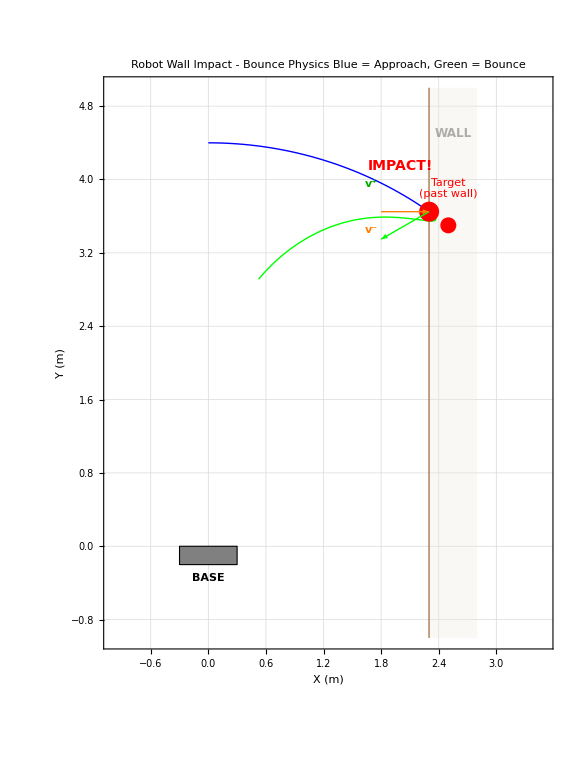

✓ Animation complete

========================================

RESULTS SUMMARY

========================================

Wall position: x = 2.3 m

Collision time: 1.56 s

Collision point: (2.3, 3.65)

Impact Physics:

e = 0.7 (restitution)

μ = 0.1 (friction)

v⁻ = (1.13, -0.86) m/s

v⁺ = (-0.79, -0.67) m/s

Energy retained: 53.1%

========================================

```mathematica
(* ========================================*)
(*ROBOT WALL IMPACT & BOUNCE*)
(*Tip hits a vertical wall*)
(* ========================================*)

ClearAll["Global`*"];

(* ========================================*)
(*1. PARAMETERS*)
(* ========================================*)

n=4;
linkLength=1.10;
baseX=0;
baseY=0;

(*Physical parameters*)
massPerLink=1.0;
linkLengthNum=1.0;
gNum=9.81;

(*Controller estimates*)
massEstimates=Table[0.8,{i,n}];

(*Home position*)
homeAngles={0,0,0,0};  (*Straight up*)

(*WALL POSITION*)
wallX=2.3;  (*Wall at x=2.0*)

(*Impact physics *)
eWall=.7;   (*Coefficient of restitution*)
muWall=0.1;  (*Coefficient of friction*)
mTip=.50;    (*Effective tip mass*)

Print["========================================"];
Print["SIMPLE ROBOT WALL BOUNCE"];
Print["========================================\n"];
Print["Wall location: x = ",wallX," m"];
Print["Restitution e = ",eWall];
Print["Friction μ = ",muWall];
Print["\n"];

(* ========================================*)
(*2. HELPER FUNCTIONS*)
(* ========================================*)

limm=0.25;
Sat[x_]:=Piecewise[{{x/limm,Abs[x]<limm},{-1,x<=-limm},{1,x>=limm}}];

SmoothStep[t_,t0_,t1_]:=Piecewise[{{0,t<t0},{1,t>t1},{(1-Cos[Pi*(t-t0)/(t1-t0)])/2,t0<=t<=t1}}];

(* ========================================*)
(*3. IMPACT PHYSICS (from ball example)*)
(* ========================================*)

ApplyWallImpact[vxMinus_,vyMinus_]:=Module[{vxPlus,vyPlus,Jn,Jt,deltaVx},Print["=== WALL IMPACT DETECTED ==="];
Print["Pre-impact:  vx⁻ = ",NumberForm[vxMinus,{4,2}]," m/s,  vy⁻ = ",NumberForm[vyMinus,{4,2}]," m/s"];
(*Normal direction is-x (wall faces left)*)(*So normal velocity is vx,tangential is vy*)(*Newton's Restitution-normal component reverses*)vxPlus=-eWall*vxMinus;
(*Coulomb Friction-affects tangential*)Jn=mTip*Abs[vxMinus]*(1+eWall);
Jt=muWall*Jn;
deltaVx=Jt/mTip;
If[Abs[vyMinus]>deltaVx,vyPlus=vyMinus-Sign[vyMinus]*deltaVx;
Print["Status: SLIDING"],vyPlus=0;
Print["Status: STICKING"]];
Print["Post-impact: vx⁺ = ",NumberForm[vxPlus,{4,2}]," m/s,  vy⁺ = ",NumberForm[vyPlus,{4,2}]," m/s"];
Print["Energy retained: ",NumberForm[100*(vxPlus^2+vyPlus^2)/(vxMinus^2+vyMinus^2),{3,1}],"%"];
Print[""];
{vxPlus,vyPlus}];

(* ========================================*)
(*4. KINEMATICS*)
(* ========================================*)

xj[0]=baseX;yj[0]=baseY;
Do[xj[i]=baseX+Sum[-linkLength*Sin[θ[j][t]],{j,1,i}],{i,1,n}];
Do[yj[i]=baseY+Sum[linkLength*Cos[θ[j][t]],{j,1,i}],{i,1,n}];

Do[xb[i]=baseX+xj[i-1]-baseX-linkLength/2*Sin[θ[i][t]],{i,1,n}];
Do[yb[i]=baseY+yj[i-1]-baseY+linkLength/2*Cos[θ[i][t]],{i,1,n}];

(*Tip position functions*)
xTip[th1_,th2_,th3_,th4_]:=baseX-linkLength*(Sin[th1]+Sin[th2]+Sin[th3]+Sin[th4]);
yTip[th1_,th2_,th3_,th4_]:=baseY+linkLength*(Cos[th1]+Cos[th2]+Cos[th3]+Cos[th4]);

(* ========================================*)
(*5. TARGET-Beyond the wall!*)
(* ========================================*)

(*Target is PAST the wall-robot will try to reach it and hit wall*)
targetX=2.5;  (*Past wall at x=2.5*)
targetY=3.5;

Print["Target: (",targetX,", ",targetY,") - PAST THE WALL!"];
Print["Robot will collide with wall while trying to reach target.\n"];

(*Solve IK*)
sol=NMinimize[{(xTip[t1,t2,t3,t4]-targetX)^2+(yTip[t1,t2,t3,t4]-targetY)^2,-Pi/2<t1<Pi/2,-Pi/2<t2<Pi/2,-Pi/2<t3<Pi/2,-Pi/2<t4<Pi/2},{t1,t2,t3,t4}];

targetAngles={t1,t2,t3,t4}/. sol[[2]];
Print["Target angles: ",Round[targetAngles*180/Pi,1],"°"];
Print["Would reach: (",Round[xTip@@targetAngles,0.01],", ",Round[yTip@@targetAngles,0.01],")\n"];

(* ========================================*)
(*6. DYNAMICS*)
(* ========================================*)

Do[Mj[i]=1/12*m[i]*l[i]^2,{i,n}];

T=Sum[1/2*m[i]*(D[xb[i],t]^2+D[yb[i],t]^2)+1/2*Mj[i]*(D[θ[i][t],t])^2,{i,n}];
V=Sum[m[i]*g*yb[i],{i,n}];
Lag=T-V;
Eqs=Table[D[D[Lag,D[θ[i][t],t]],t]-D[Lag,θ[i][t]],{i,n}];

MassM=Table[Coefficient[Eqs[[i]],D[θ[j][t],{t,2}]],{i,n},{j,n}];
Cc=Table[Sum[0.5*(D[MassM[[i,j]],θ[k][t]]+D[MassM[[i,k]],θ[j][t]]-D[MassM[[j,k]],θ[i][t]])*D[θ[k][t],t],{k,n}],{i,n},{j,n}];
Gg=Table[D[Eqs[[i]],g],{i,n}]*g;

(* ========================================*)
(*7. CONTROLLER*)
(* ========================================*)

q=Table[θ[i][t],{i,n}];
Λ=DiagonalMatrix[Table[4,{i,n}]];
controlGains=DiagonalMatrix[Table[10.0,{i,n}]];

numRules:=Join[Table[m[i]->massPerLink,{i,n}],Table[l[i]->linkLengthNum,{i,n}],{g->gNum}];

(* ========================================*)
(*8. PHASE 1-APPROACH (hit wall)*)
(* ========================================*)

Print["========================================"];
Print["PHASE 1: Approaching wall"];
Print["========================================\n"];

tApproach=2.0;

qdes1=Table[Piecewise[{{homeAngles[[i]]+(targetAngles[[i]]-homeAngles[[i]])*SmoothStep[t,0,tApproach],True}}],{i,n}];

qtilde1=q-qdes1;
dqr1=D[qdes1,t]-Λ.qtilde1;
s1=D[qtilde1,t]+Λ.qtilde1;

DynamicsLHS1=MassM.D[dqr1,t]+Cc.dqr1+Gg;
Yy1=Table[D[DynamicsLHS1[[i]],m[j]],{i,n},{j,n}];
SatVec1=Table[Sat[s1[[i]]],{i,n}];
ControlInput1=Yy1.massEstimates-controlGains.SatVec1;

ics1=Join[Table[θ[i][0]==homeAngles[[i]],{i,n}],Table[Derivative[1][θ[i]][0]==0,{i,n}]];

EqsN1=Thread[Eqs==ControlInput1]/. numRules;

solDE1=NDSolve[Join[EqsN1,ics1],Table[θ[i][t],{i,n}],{t,0,tApproach},Method->{"EquationSimplification"->"Residual"},MaxSteps->10000];

Print["✓ Approach complete\n"];

(* ========================================*)
(*9. DETECT COLLISION*)
(* ========================================*)

Print["Checking for wall collision..."];

(*Find when tip crosses wall*)
collisionTime=None;
collisionY=None;

Do[Module[{xTipNow,yTipNow},xTipNow=(xj[n]/. solDE1/. t->time)[[1]];
yTipNow=(yj[n]/. solDE1/. t->time)[[1]];
If[xTipNow>=wallX&&collisionTime===None,collisionTime=time;
collisionY=yTipNow;];],{time,0,tApproach,0.01}];

If[collisionTime=!=None,Print["*** COLLISION at t = ",NumberForm[collisionTime,{3,2}]," s ***"];
Print["    Position: (",wallX,", ",NumberForm[collisionY,{3,2}],")\n"];
(*Get velocity at collision*)dt=0.02;
xBefore=(xj[n]/. solDE1/. t->(collisionTime-dt))[[1]];
yBefore=(yj[n]/. solDE1/. t->(collisionTime-dt))[[1]];
vxMinus=(wallX-xBefore)/dt;
vyMinus=(collisionY-yBefore)/dt;
(*Apply impact physics*){vxPlus,vyPlus}=ApplyWallImpact[vxMinus,vyMinus];
(*Angles at collision*)collisionAngles=Table[(θ[i][t]/. solDE1[[1]]/. t->collisionTime),{i,n}];
collisionVels=Table[(D[θ[i][t]/. solDE1[[1]],t]/. t->collisionTime),{i,n}];,Print["No collision detected."];];

(* ========================================*)
(*10. PHASE 2-BOUNCE BACK*)
(* ========================================*)

If[collisionTime=!=None,Print["========================================"];
Print["PHASE 2: Bouncing back"];
Print["========================================\n"];
(*New target-back towards home,reflecting the bounce*)bounceTargetX=0.5;(*Bounce back to left*)bounceTargetY=collisionY+vyPlus*1.0;(*Continue in y direction*)Print["Bounce target: (",bounceTargetX,", ",NumberForm[bounceTargetY,{3,2}],")\n"];
(*IK for bounce target*)solBounce=NMinimize[{(xTip[t1,t2,t3,t4]-bounceTargetX)^2+(yTip[t1,t2,t3,t4]-bounceTargetY)^2,-Pi/2<t1<Pi/2,-Pi/2<t2<Pi/2,-Pi/2<t3<Pi/2,-Pi/2<t4<Pi/2},{t1,t2,t3,t4}];
bounceAngles={t1,t2,t3,t4}/. solBounce[[2]];
tBounce=2.0;
(*Trajectory from collision angles to bounce target*)qdes2=Table[Piecewise[{{collisionAngles[[i]]+(bounceAngles[[i]]-collisionAngles[[i]])*SmoothStep[t,0,tBounce],True}}],{i,n}];
qtilde2=q-qdes2;
dqr2=D[qdes2,t]-Λ.qtilde2;
s2=D[qtilde2,t]+Λ.qtilde2;
DynamicsLHS2=MassM.D[dqr2,t]+Cc.dqr2+Gg;
Yy2=Table[D[DynamicsLHS2[[i]],m[j]],{i,n},{j,n}];
SatVec2=Table[Sat[s2[[i]]],{i,n}];
ControlInput2=Yy2.massEstimates-controlGains.SatVec2;
(*Start from collision state*)ics2=Join[Table[θ[i][0]==collisionAngles[[i]],{i,n}],Table[Derivative[1][θ[i]][0]==collisionVels[[i]],{i,n}]];
EqsN2=Thread[Eqs==ControlInput2]/. numRules;
Print["Simulating bounce..."];
solDE2=NDSolve[Join[EqsN2,ics2],Table[θ[i][t],{i,n}],{t,0,tBounce},Method->{"EquationSimplification"->"Residual"},MaxSteps->10000];
Print["✓ Bounce complete\n"];];

(* ========================================*)
(*11. VISUALIZATION*)
(* ========================================*)

Print["========================================"];
Print["CREATING PLOTS"];
Print["========================================\n"];

(*Wall graphic*)
wallGraphic=Graphics[{Thick,Brown,Line[{{wallX,-1},{wallX,5}}],LightBrown,Opacity[0.3],Rectangle[{wallX,-1},{wallX+0.5,5}],Black,Text[Style["WALL",Bold,12],{wallX+0.25,4.5}]}];

(*Base*)
baseGraphic=Graphics[{Gray,EdgeForm[Black],Rectangle[{baseX-0.3,baseY-0.2},{baseX+0.3,baseY}],Black,Text[Style["BASE",Bold],{baseX,baseY-0.35}]}];

(*Target*)
targetGraphic=Graphics[{Red,PointSize[0.02],Point[{targetX,targetY}],Text["Target\n(past wall)",{targetX,targetY+0.4}]}];

(*Phase 1 trajectory*)
traj1=ParametricPlot[{xj[n],yj[n]}/. solDE1,{t,0,collisionTime},PlotStyle->{Thick,Blue},PlotRange->All];

(*Phase 2 trajectory*)
traj2=If[collisionTime=!=None,ParametricPlot[{xj[n],yj[n]}/. solDE2,{t,0,tBounce},PlotStyle->{Thick,Green},PlotRange->All],Graphics[{}]];

(*Impact marker*)
impactMarker=If[collisionTime=!=None,Graphics[{(*Impact point*)Red,PointSize[0.025],Point[{wallX,collisionY}],(*Velocity arrows*)Orange,Thick,Arrowheads[0.04],Arrow[{{wallX-0.5,collisionY},{wallX,collisionY}}],(*v⁻ into wall*)Green,Thick,Arrowheads[0.04],Arrow[{{wallX,collisionY},{wallX-0.5,collisionY+0.3*Sign[vyPlus]}}],(*v⁺ bouncing*)Black,Text[Style["v⁻",Bold,Orange],{wallX-0.6,collisionY-0.2}],Text[Style["v⁺",Bold,Darker[Green]],{wallX-0.6,collisionY+0.3}],Text[Style["IMPACT!",Bold,Red,14],{wallX-0.3,collisionY+0.5}]}],Graphics[{}]];

(*Combined static plot*)
staticPlot=Show[wallGraphic,baseGraphic,targetGraphic,traj1,traj2,impactMarker,PlotRange->{{-1,3.5},{-1,5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->Style["Robot Wall Impact - Bounce Physics\nBlue = Approach, Green = Bounce",Bold,14],ImageSize->Large,GridLines->Automatic];

Print["✓ Static plot"];
staticPlot

(* ========================================*)
(*12. ANIMATION*)
(* ========================================*)

tTotal=If[collisionTime=!=None,collisionTime+tBounce,tApproach];

getAngles[time_]:=If[time<collisionTime,(*Phase 1*)Table[(θ[i][t]/. solDE1[[1]]/. t->time),{i,n}],(*Phase 2*)Table[(θ[i][t]/. solDE2[[1]]/. t->(time-collisionTime)),{i,n}]];

robotGraphics[time_?NumericQ]:=Module[{angles,xPos,yPos,links,joints,tipColor},angles=getAngles[time];
xPos=Table[baseX-linkLength*Sum[Sin[angles[[j]]],{j,1,k}],{k,0,n}]/. {Sum[_,{_,1,0}]->0};
xPos=Prepend[Table[baseX-linkLength*Sum[Sin[angles[[j]]],{j,1,k}],{k,1,n}],baseX];
yPos=Prepend[Table[baseY+linkLength*Sum[Cos[angles[[j]]],{j,1,k}],{k,1,n}],baseY];
(*Color:Blue normally,Red at impact,Green bouncing*)tipColor=Which[Abs[time-collisionTime]<0.1,Red,time>collisionTime,Darker[Green],True,Blue];
links=Table[{Thickness[0.012],Black,Line[{{xPos[[k]],yPos[[k]]},{xPos[[k+1]],yPos[[k+1]]}}]},{k,1,n}];
joints=Table[{Blue,Disk[{xPos[[k]],yPos[[k]]},0.06]},{k,1,n+1}];
Graphics[{links,joints,{tipColor,PointSize[0.025],Point[{xPos[[n+1]],yPos[[n+1]]}]}}]];

animation=Animate[Module[{phase},phase=If[time<collisionTime,"APPROACHING","BOUNCING"];
Show[wallGraphic,baseGraphic,robotGraphics[time],(*Show impact marker near collision*)If[Abs[time-collisionTime]<0.2,Graphics[{Red,PointSize[0.03],Point[{wallX,collisionY}],Text[Style["IMPACT!",Bold,Red,16],{wallX-0.5,collisionY+0.3}]}],Graphics[{}]],PlotRange->{{-1,3.5},{-1,5}},AspectRatio->Automatic,Frame->True,FrameLabel->{"X (m)","Y (m)"},PlotLabel->Style["Robot Wall Bounce\nt = "<>ToString[NumberForm[time,{3,2}]]<>" s - "<>phase<>"\ne = "<>ToString[eWall]<>", μ = "<>ToString[muWall],Bold,12],ImageSize->Large]],{time,0,tTotal,0.02},AnimationRate->0.5];

Print["✓ Animation complete\n"];

Print["========================================"];
Print["RESULTS SUMMARY"];
Print["========================================"];
Print["Wall position: x = ",wallX," m"];
Print["Collision time: ",NumberForm[collisionTime,{3,2}]," s"];
Print["Collision point: (",wallX,", ",NumberForm[collisionY,{3,2}],")"];
Print[""];
Print["Impact Physics:"];
Print["  e = ",eWall," (restitution)"];
Print["  μ = ",muWall," (friction)"];
Print["  v⁻ = (",NumberForm[vxMinus,{4,2}],", ",NumberForm[vyMinus,{4,2}],") m/s"];
Print["  v⁺ = (",NumberForm[vxPlus,{4,2}],", ",NumberForm[vyPlus,{4,2}],") m/s"];
Print["  Energy retained: ",NumberForm[100*(vxPlus^2+vyPlus^2)/(vxMinus^2+vyMinus^2),{3,1}],"%"];
Print["========================================\n"];

animation
```